Construct rank-deficient matrix Z=U V+δZ where
	Z_(m×n)	nearly rank deficient
	U_(m×r)	left vectors
	V_(r×n)	right vectors
	δZ_(m×n)	random error term
	r<min{m,n} is the rank
The effective rank of Z should be r
This is illustrated by showing that only the largest r singular values are significant
For example:

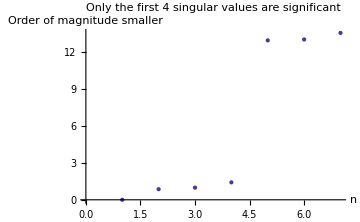

```mathematica
ClearAll[m,r,n,U0,V0,Z]
{m,r,n}={9,4,7};
U0=RandomReal[{0,10},{m,r}];
V0=RandomReal[{0,10},{r,n}];
Z=U0.V0+RandomReal[{0,10^-10},{m,n}];
SingularValueList[Z]//#/#⟦1⟧&//-Log@Abs[#]/Log[10]&//ListPlot[#,AxesLabel->{"n","Order of magnitude smaller"},ImageSize->Medium,PlotLabel->"Only the first "<>ToString[r]<>" singular values are significant"]&
```

However, SVD needs the completion of the matrix Z in the first place
In practice, Z is often too large to be constructed compeletly
Use the adpative crossing approximation (ACA) method [Bebendorf 2001-2003] to approximate the Z without a complete construction of Z
The actual implementation of the algorithm is implemented in accordance to [ZHAO etc. 2005 Nov] Section IV Part C

```mathematica
ClearAll[ROW,COL,R,U,V,u,v,Zp,ZpNorm2,FNorm,MaxPos,eps]
Zp=ConstantArray[0.0,{m,n}];
R=ConstantArray[0.0,{m,n}];
R⟦1⟧=Z⟦1⟧;
ROW={1};
MaxPos[a_]:=a//Position[#,Max[#]]⟦1,1⟧&;
COL={MaxPos[Z⟦1⟧]}
v=Z⟦1⟧/Z⟦1,COL⟦1⟧⟧;
R⟦All,1⟧=Z⟦All,COL⟦1⟧⟧;
u=Z⟦All,COL⟦1⟧⟧;

FNorm[a_]:=Norm[a,"Frobenius"]
ZpNorm2=FNorm[Zp]^2+FNorm[u]^2 FNorm[v]^2;
AppendTo[ROW,MaxPos[Z⟦All,COL⟦1⟧⟧]]
```

{4}

{1,1}

Cross approximation with full pivoting and quadratic complexity O(r m n)

```mathematica
ClearAll[MaxValueLocation]
(*Non-compiled version of locating maximal element in a matrix*)
MaxValueLocation[a_]:=Module[{i,j,i0,j0,m,n,max},
{m,n}=Dimensions[a];
{i0,j0}={1,1};
max=a⟦1,1⟧;
For[i=1,i≤m,i++,
For[j=1,j≤n,j++,
If[a⟦i,j⟧>max,
{i0,j0}={i,j};
max=a⟦i0,j0⟧;
];
];
];
{i0,j0}
]
(*Compiled version of locating maximal element in a matrix*)
MaxValueLocationC=Compile[{{a,_Real,2}},
Module[{i,j,i0,j0,m,n,max},
{m,n}=Dimensions[a];
{i0,j0}={1,1};
max=a⟦1,1⟧;
For[i=1,i≤m,i++,
For[j=1,j≤n,j++,
If[a⟦i,j⟧>max,
{i0,j0}={i,j};
max=a⟦i0,j0⟧;
];
];
];
{i0,j0}
]
];
ClearAll[i]
For[i=1,i≤10000,i++,MaxValueLocation[Z];]//AbsoluteTiming//#⟦1⟧&//Print
For[i=1,i≤10000,i++,MaxValueLocationC[Z];]//AbsoluteTiming//#⟦1⟧&//Print
```

0.95884

0.05796

```mathematica
ClearAll[ν,i0,j0,A,B,R]
eps=1.0 10^-4;
R=Z;
A={};
B={};
For[ν=1,ν≤10,ν++,
{i0,j0}=MaxValueLocationC[R];
If[Abs[R⟦i0,j0⟧]<eps,Print["Terminate: rank=",ν-1,", Abs[Max[R]]=",Abs[R⟦i0,j0⟧]];Break[];];
AppendTo[A,R⟦All,j0⟧];
AppendTo[B,R⟦i0⟧/R⟦i0,j0⟧];
R=R-Outer[Times,A⟦ν⟧,B⟦ν⟧];
];
Print["Check accuracy: Norm[Z-∑_ν a bᵀ]=",Z-∑_(ν=1)^Length[A] Outer[Times,A⟦ν⟧,B⟦ν⟧]//Norm];
```

Terminate: rank=4, Abs[Max[R]]=5.76642×10^-11

Check accuracy: Norm[Z-∑_ν a bᵀ]=1.4931×10^-10

Cross approximation with partial pivoting

```mathematica
ClearAll[MaxValueLocationVC]
MaxValueLocationVC=Compile[{{a,_Real,1},{exlList,_Integer,1}},
Module[{i,i0,m,max},
m=Length[a];
i0=1;
max=a⟦1⟧;
For[i=1,i≤m,i++,
If[MemberQ[exlList,i],Continue[];];
If[a⟦i⟧>max,
i0=i;
max=a⟦i0⟧;
];
];
i0
]
];
ClearAll[i]
For[i=1,i≤10000,i++,MaxValueLocationVC[Z⟦1⟧,{}];]//AbsoluteTiming//#⟦1⟧&//Print
```

0.0363

```mathematica
ClearAll[μ,ν,k,i0,j0,A,B,δ,R,a,b,ROW]
eps=1.0 10^-4;
R=Z;
i0=1;
ROW={};
A={};
B={};
For[ν=1,ν≤2,ν++,
AppendTo[ROW,i0];
j0=MaxValueLocationVC[Z⟦ROW⟦1⟧⟧,{}];
δ=R⟦i0,j0⟧-∑_(μ=1)^(ν-1) A⟦μ,i0⟧B⟦μ,j0⟧;
Print[δ];
If[Abs[δ]<eps,Print["Terminate; rank=",ν-1,", residual=",Abs[δ]];Break[];];
a=R⟦All,j0⟧-∑_(μ=1)^(ν-1) A⟦μ⟧B⟦μ,j0⟧;
b=R⟦i0⟧-∑_(μ=1)^(ν-1) A⟦μ,i0⟧B⟦μ⟧;
AppendTo[A,a];
AppendTo[B,b/δ];
i0=MaxValueLocationVC[Abs[b],ROW];
i0
];
```

176.179

0.

Terminate; rank=1, residual=0.

```mathematica
If[Element[1,Range[4]],Print["OK"]];
```